```mathematica
14 12
```

168

```mathematica
CONTROLLER.mouseController.pressed_M(new Point(2,5));
CONTROLLER.mouseController.dragged_M(new Point(1,5));
CONTROLLER.mouseController.dragged_M(new Point(1,10));
CONTROLLER.mouseController.dragged_M(new Point(12,5));
CONTROLLER.mouseController.dragged_M(new Point(2,5));
CONTROLLER.mouseController.released_M();

CONTROLLER.mouseController.pressed_M(new Point(3,0));
CONTROLLER.mouseController.dragged_M(new Point(3,7));
CONTROLLER.mouseController.released_M();
```

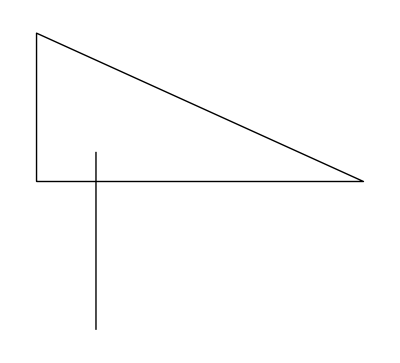

```mathematica
Graphics[{Line[{{1,5},{1,10},{12,5},{1,5}}],Line[{{3,0},{3,6}}]}]
```

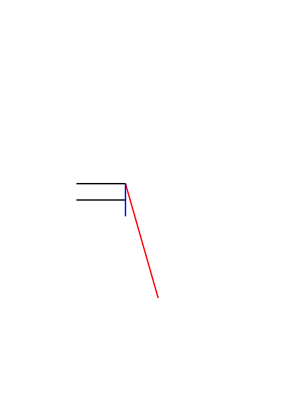

```mathematica
Graphics[{Red,Line[{{21,11},{23,4}}],Black,Line[{{18,11},{21,11}}],Line[{{18,10},{21,10}}],Blue,Line[{{21,11},{21,10}}],Line[{{21,10},{21,9}}]},PlotRange->{{15,30},{0,20}}]
```

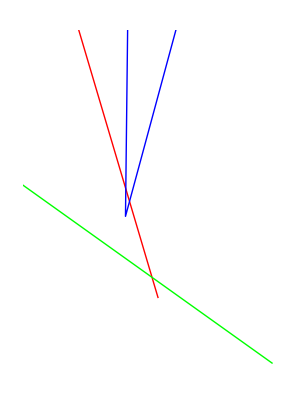

```mathematica
Graphics[{Red,Line[{{7,58},{23,4}}],Green,Line[{{30,0},{9,15}}],Blue,Line[{{22,96},{21,12}}]{21,9},{44,94}}]},PlotRange->{{15,30},{0,20}}]
```

[PTBA: <815.0, 365.0> 0.0, PTBA: <815.375, 364.75> 0.041666666666666664, PTBA: <824.0, 359.0> 1.0]

```mathematica
12+0.4375(1-12)
```

7.1875

### before

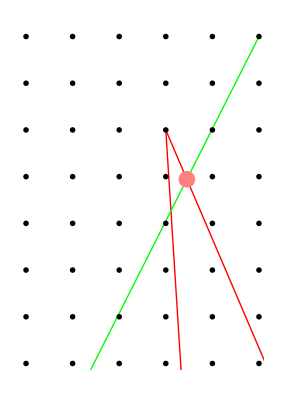

```mathematica
Graphics[{Red,Line[{{73,26},{43,96},{46,49}}],Green,Line[{{45,98},{5,19}}],Pink,PointSize[0.03],Point[{43.4526,94.94390}],Black,PointSize[0.01],Table[Point[{i,j}],{i,40,50},{j,90,100}]},PlotRange->{{43-3,43+2},{96-5,96+2}}]
```

### after

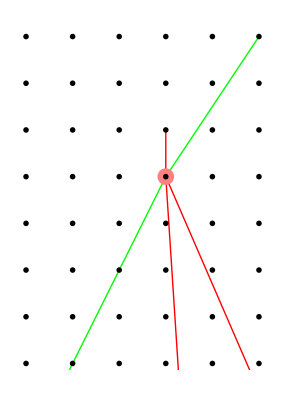

```mathematica
Graphics[{Red,Line[{{43,96},{43,95},{46,49}}],Line[{{43,95},{73,26}}],Green,Line[{{45,98},{43,95}}],Line[{{43,95},{5,19}}],Pink,PointSize[0.03],Point[{43,95}],Black,PointSize[0.01],Table[Point[{i,j}],{i,40,50},{j,90,100}]},PlotRange->{{43-3,43+2},{96-5,96+2}}]
```

### before

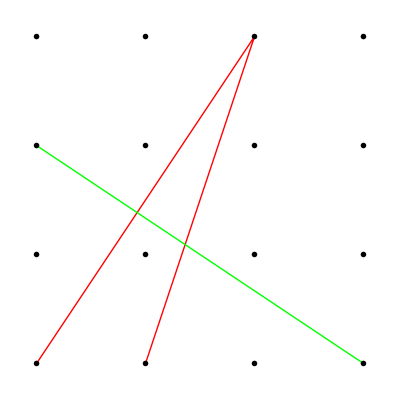

```mathematica
Graphics[{Red,Line[{{0,0},{2, 3},{1,0}}],Green,Line[{{3,0},{0,2}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,0,3},{j,0,3}]}]
```

### before

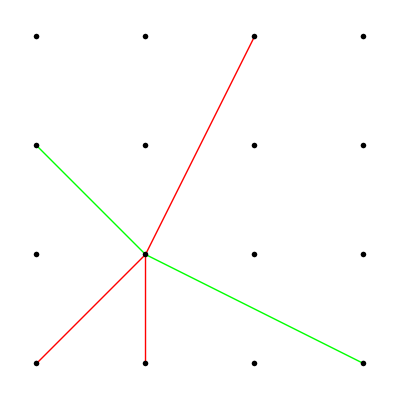

```mathematica
Graphics[{Red,Line[{{0,0},{1,1}}],Line[{{1,1},{2, 3}}],Line[{{1,1},{1,0}}],Green,Line[{{3,0},{1,1},{0,2}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,0,3},{j,0,3}]}]
```

## ColinearBug2

### before

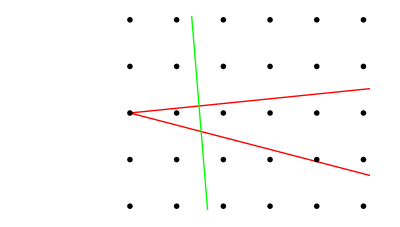

```mathematica
Graphics[{Red,Line[{{60,78},{1,72},{47,60}}],Green,Line[{{7,17},{2,78}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,1,60},{j,17,78}]},PlotRange->{{1-2,1+5},{72-2,72+2}}]
```

### after

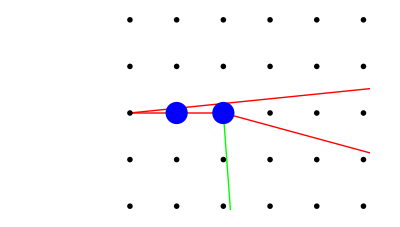

```mathematica
Graphics[{Red,Line[{{60,78},{1,72}}],Line[{{1,72},{2,72}}],Line[{{3,72},{47,60}}],Line[{{2,72},{3,72}}],Green,Line[{{7,17},{3,72}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,1,60},{j,17,78}],Blue,PointSize[0.04],Point[{3,72}],Point[{2,72}]},PlotRange->{{1-2,1+5},{72-2,72+2}}]
```

## ColinearBug4

CONTROLLER.mouseController.pressed_M(new Point(21, 11));
CONTROLLER.mouseController.dragged_M(new Point(23, 4));
CONTROLLER.mouseController.released_M(false);
		
CONTROLLER.mouseController.pressed_M(new Point(18, 11));
CONTROLLER.mouseController.dragged_M(new Point(21, 11));
CONTROLLER.mouseController.released_M(false);
		
CONTROLLER.mouseController.pressed_M(new Point(21, 11));
CONTROLLER.mouseController.dragged_M(new Point(21, 9));
CONTROLLER.mouseController.released_M(false);
		
ONTROLLER.mouseController.pressed_M(new Point(21, 9));
CONTROLLER.mouseController.dragged_M(new Point(44, 94));
CONTROLLER.mouseController.released_M(false);

### before

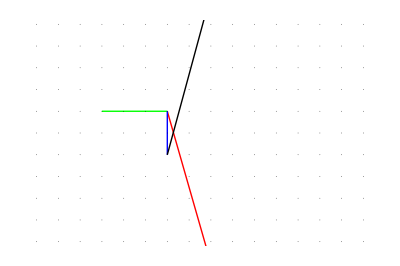

```mathematica
Graphics[{Red,Line[{{21,11},{23,4}}],Green,Line[{{18,11},{21,11}}],Blue,Line[{{21,11},{21,9}}],Black,Line[{{21,9},{44,94}}],Black,PointSize[0.001],Table[Point[{i,j}],{i,1,60},{j,0,20}]},PlotRange->{{15,30},{5,15}}]
```

### after

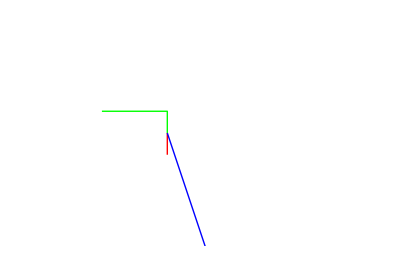

```mathematica
Graphics[{Red,Line[{{21,10},{21,9}}],Green,Line[{{18,11},{21,11},{21,10}}],Blue,Line[{{21,10},{23,4}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,1,60},{j,17,78}],Blue,PointSize[0.04],Point[{3,72}],Point[{2,72}]},PlotRange->{{15,30},{5,15}}]
```

## XBCEqual0

CONTROLLER.mouseController.pressed_M(new Point(45, 47));
CONTROLLER.mouseController.dragged_M(new Point(7, 41));
CONTROLLER.mouseController.released_M(false);
		
CONTROLLER.mouseController.pressed_M(new Point(7, 41));
CONTROLLER.mouseController.dragged_M(new Point(45, 81));
CONTROLLER.mouseController.released_M(false);

CONTROLLER.mouseController.pressed_M(new Point(13, 56));
CONTROLLER.mouseController.dragged_M(new Point(4, 17));
CONTROLLER.mouseController.released_M(false);

CONTROLLER.mouseController.pressed_M(new Point(25, 62));
CONTROLLER.mouseController.dragged_M(new Point(3, 34));
CONTROLLER.mouseController.released_M(false);

### before

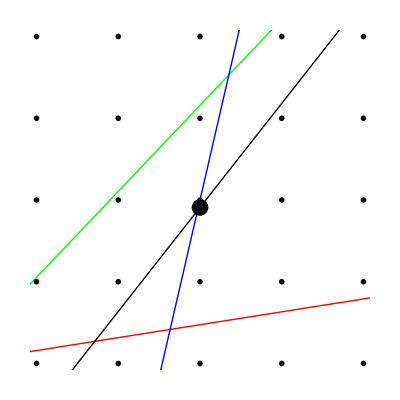

```mathematica
Graphics[{Red,Line[{{45,47},{7,41}}],Green,Line[{{7,41},{45,81}}],Blue,Line[{{13,56},{4,17}}],Black,Line[{{25,62},{3,34}}],Black,PointSize[0.03],Point[{10.000000000000002,42.90909090909091}],PointSize[0.01],Table[Point[{i,j}],{i,3,45},{j,17,81}]},PlotRange->{{10-2,10+2},{43-2,43+2}}]
```

### after

```mathematica
Graphics[{Red,Line[{{60,78},{1,72}}],Line[{{1,72},{2,72}}],Line[{{3,72},{47,60}}],Line[{{2,72},{3,72}}],Green,Line[{{7,17},{3,72}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,1,60},{j,17,78}],Blue,PointSize[0.04],Point[{3,72}],Point[{2,72}]},PlotRange->{{1-2,1+5},{72-2,72+2}}]
```

-Graphics-

## testE1EdgesSizeEquals2Bug

CONTROLLER.mouseController.pressed_M(new Point(39, 26));
		CONTROLLER.mouseController.dragged_M(new Point(81, 96));
		CONTROLLER.mouseController.dragged_M(new Point(82, 24));
		CONTROLLER.mouseController.dragged_M(new Point(26, 57));
		CONTROLLER.mouseController.dragged_M(new Point(85, 23));
		CONTROLLER.mouseController.released_M(false);

		CONTROLLER.mouseController.pressed_M(new Point(99, 38));
		CONTROLLER.mouseController.dragged_M(new Point(37, 38));
		CONTROLLER.mouseController.released_M(false);

### before

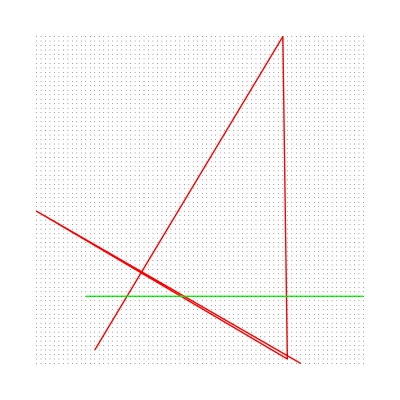

```mathematica
Graphics[{Red,Line[{{39,26},{81,96},{82,24},{26,57},{85,23}}],Green,Line[{{99,38},{37,38}}],Black,PointSize[0.03],PointSize[0.001],Table[Point[{i,j}],{i,26,99},{j,23,96}]},PlotRange->{{26,99},{23,96}}]
```

### script

```mathematica
addSegment[a_,b_]:=(
segs=segs~Append~{a,b};
Graphics[{Line/@segs,PointSize[0.01],Point[{49,44}],Point[{49,43}],PointSize[0.001],Table[Point[{i,j}],{i,26,99},{j,23,96}]},PlotRange->{{35,65},{30,60}}]
)
```

```mathematica
removeSegment[a_,b_]:=(
segs=DeleteCases[segs,{a,b}];
Graphics[{Line/@segs,PointSize[0.01],Point[{49,44}],Point[{49,43}],PointSize[0.001],Table[Point[{i,j}],{i,26,99},{j,23,96}]},PlotRange->{{35,65},{30,60}}]
)
```

```mathematica
segs={}
```

{}

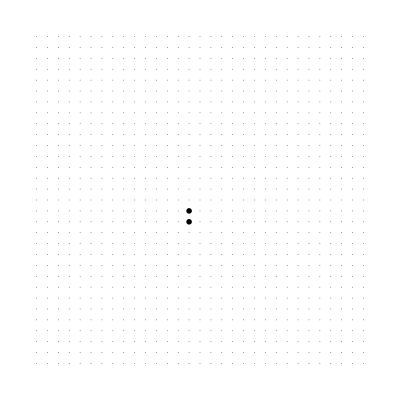

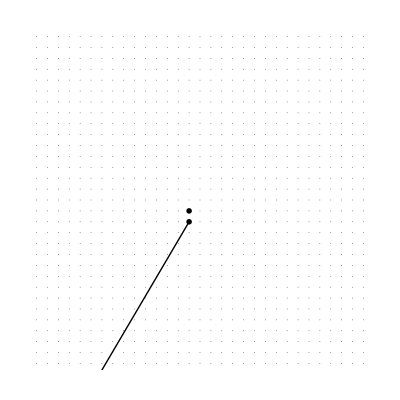

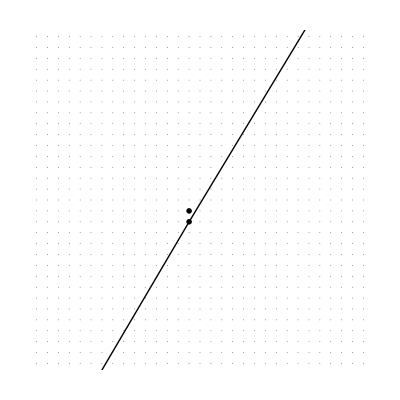

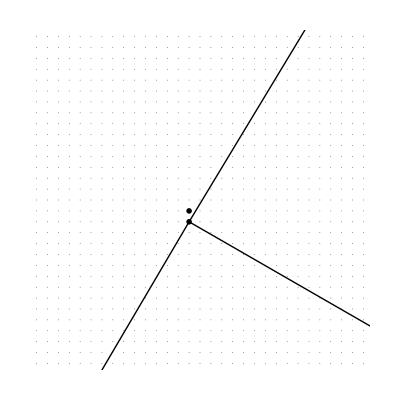

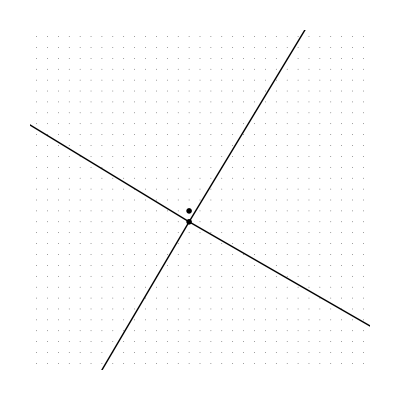

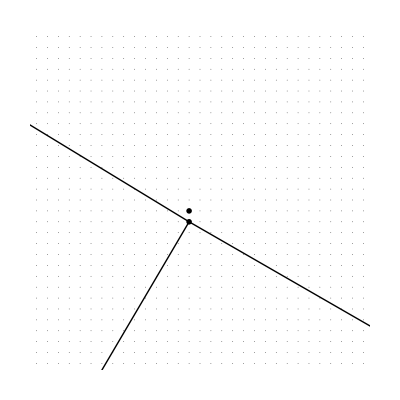

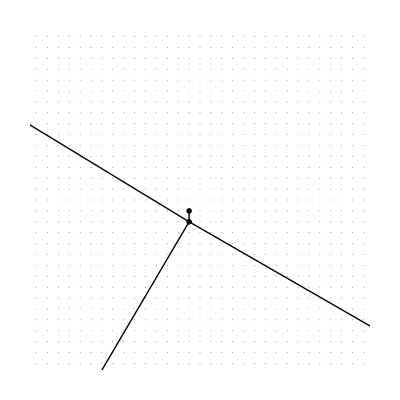

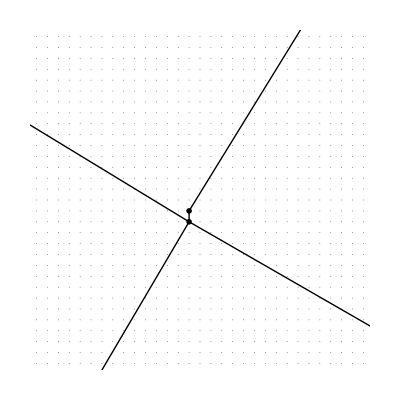

-Graphics-

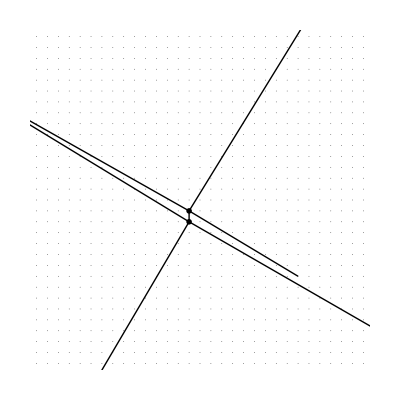

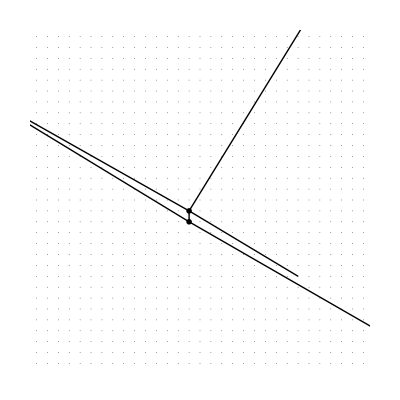

```mathematica
addSegment[{81, 96}, {82, 24}]
addSegment[{39, 26}, {49,43}]
addSegment[{49,43}, {81, 96}]
addSegment[{82, 24}, {49,43}]
addSegment[{49,43}, {26, 57}]

removeSegment[{49,43}, {81, 96}]

addSegment[{49, 43}, {49,44}]
addSegment[{49, 44}, {81, 96}]
addSegment[{26, 57}, {49,44}]
addSegment[{82,25}, {85, 23}]
addSegment[{49, 44}, {59, 38}]
removeSegment[{39, 26}, {49, 43}]
```

```mathematica
Line/@segs
```

{Line[{{81,96},{82,24}}],Line[{{82,24},{49,43}}],Line[{{49,43},{26,57}}],Line[{{49,43},{49,44}}],Line[{{49,44},{81,96}}],Line[{{26,57},{49,44}}],Line[{{82,25},{85,23}}],Line[{{49,44},{59,38}}]}

```mathematica
{{81,96},{82,24}},{{82,24},{49,43}},{{49,43},{26,57}},{{49,43},{49,44}},{{49,44},{81,96}},{{26,57},{49,44}},{{82,25},{85,23}},{{49,44},{59,38}}}
```

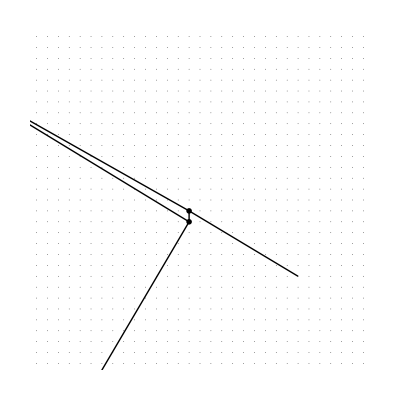

```mathematica
Graphics[{Line[{{39,26},{49,43}}],
Line[{{82,25},{85,23}}],
Line[{{49,43},{26,57},{49,44}}],
Line[{{49,44},{49,43}}],
Line[{{49,44},{59,38}}],

PointSize[0.01],Point[{49,44}],Point[{49,43}],PointSize[0.001],Table[Point[{i,j}],{i,26,99},{j,23,96}]},PlotRange->{{35,65},{30,60}}]
```

## testBug1

### before

```mathematica
Graphics[{Red,Line[{{52,8},{30,65}}],Green,Line[{{51,35},{34,74},{66,99},{11,22}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,1,60},{j,17,78}]},PlotRange->{{1-2,1+5},{72-2,72+2}}]
```

-Graphics-

## testNoEdgesShouldIntersectBug1

CONTROLLER.mouseController.pressed_M(new Point(73, 26));
		CONTROLLER.mouseController.dragged_M(new Point(43, 96));
		CONTROLLER.mouseController.dragged_M(new Point(46, 49));
		CONTROLLER.mouseController.released_M(false);

		CONTROLLER.mouseController.pressed_M(new Point(45, 98));
		CONTROLLER.mouseController.dragged_M(new Point(5, 19));
		CONTROLLER.mouseController.released_M(false);

### before

```mathematica
Line[{{45,98},{5,19}}]
```

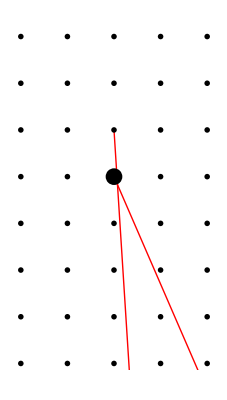

```mathematica
Graphics[{Red,Line[{{43,96},{46,49}}],Line[{{73,26},{43,95}}],Green,Black,PointSize[0.03],Point[{43,95}],PointSize[0.01],Table[Point[{i,j}],{i,5,73},{j,19,98}]},PlotRange->{{43-2,43+2},{96-5,96+2}}]
```

## testBug2

### before

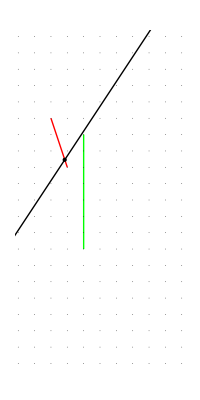

```mathematica
Graphics[{Red,
Line[{{42,45},{43,42}}],Green,Line[{{44,44},{44,37}}],Black,Line[{{30,23},{63.0,73.0}}],Point[{42.84,42.46}],PointSize[0.001],Table[Point[{i,j}],{i,30,63},{j,23,73}]},PlotRange->{{40,50},{30,50}}]
```

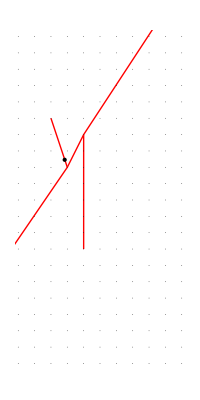

```mathematica
Graphics[{Red,
Line[{{30,23},{43,42}}],
Line[{{42,45},{43,42}}],
Line[{{43,42},{44,44}}],
Line[{{44,44},{44,37}}],
Line[{{44,44},{63.0,73.0}}],
Green,Black,Point[{42.84,42.46}],PointSize[0.001],Table[Point[{i,j}],{i,30,63},{j,23,73}]},PlotRange->{{40,50},{30,50}}]
```

## testBug3

### before

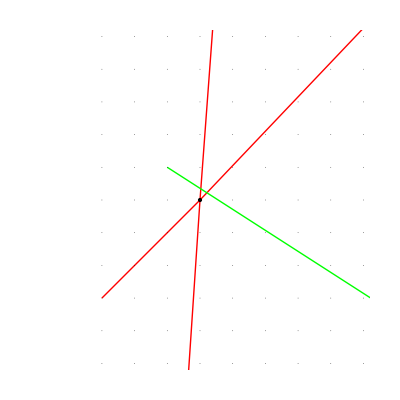

```mathematica
Graphics[{Red,
Line[{{40,19},{41,34}}],Line[{{41,34},{43,61}}],Line[{{99,95},{41,34}}],Line[{{41,34},{38,31}}],Green,Line[{{40,35},{82,8}}],Black,Point[{41,34}],PointSize[0.001],Table[Point[{i,j}],{i,38,99},{j,8,95}]},PlotRange->{{41-5,41+5},{34-5,34+5}}]
```

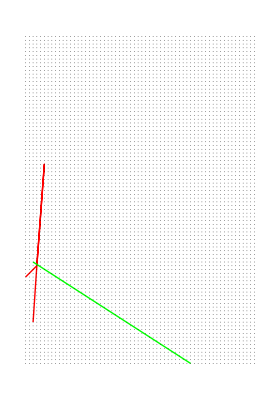

```mathematica
Graphics[{Red,
Line[{{40,19},{41,34}}],Line[{{41,34},{43,61},{41,34}}],Line[{{41,34},{38,31}}],Green,Line[{{40,35},{82,8}}],Black,PointSize[0.001],Table[Point[{i,j}],{i,38,99},{j,8,95}]}]
```

## testBug4

CONTROLLER.mouseController.pressed_M(new Point(351, 140));
		CONTROLLER.mouseController.dragged_M(new Point(454, 11));
		CONTROLLER.mouseController.released_M(false);
		
		CONTROLLER.mouseController.pressed_M(new Point(454, 11));
		CONTROLLER.mouseController.dragged_M(new Point(436, 146));
		CONTROLLER.mouseController.released_M(false);
		
		CONTROLLER.mouseController.pressed_M(new Point(389, 36));
		CONTROLLER.mouseController.dragged_M(new Point(462, 273));
		CONTROLLER.mouseController.released_M(false);
		
		CONTROLLER.mouseController.pressed_M(new Point(216, 161));
		CONTROLLER.mouseController.dragged_M(new Point(491, 36));
		CONTROLLER.mouseController.released_M(false);

### before

```mathematica
Table[Point[{i,j}],{i,402-5,402+5},{j,77-5,77+5}]
```

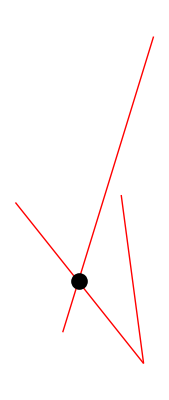

```mathematica
Graphics[{Red,
Line[{{351,140},{454,11}}],
Line[{{454,11},{436,146}}],
Line[{{389,36},{462,273}}],
Green,
Black,PointSize[0.03],Point[{402,77}],PointSize[0.01]}]
```

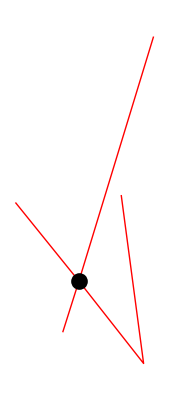

```mathematica
Graphics[{Red,
Line[{{351,140},{402,77}}],
Line[{{402,77},{454,11},{436,146}}],
Line[{{389,36},{402,77}}],
Line[{{402,77},{462,273}}],
Green,
Black,PointSize[0.03],Point[{402,77}],PointSize[0.01]}]
```

## testBug5

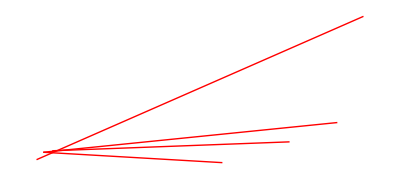

```mathematica
Graphics[{Red,
Line[{{463,221},{25,28}}],
Line[{{274,24},{34,38}}],
Line[{{34,38},{428,78}}],
Line[{{46,40},{364,52}}],
Green,
Black,PointSize[0.03],PointSize[0.01]}]
```

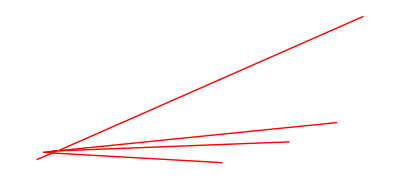

```mathematica
Graphics[{Red,
Line[{{46,37},{25,28}}],
Line[{{274,24},{46,37}}],
Line[{{46,37}, {34,38}, {53,40}}],
Line[{{53,40},{46,37}}],
Line[{{53,40},{54,40}}],
Line[{{54,40},{428,78}}],
Line[{{463,221},{54,40}}],
Line[{{46,40},{53,40}}],
Line[{{54,40}, {57,40}, {364,52}}],
Green,
Black,PointSize[0.03],PointSize[0.01]}]
```

## testBug7

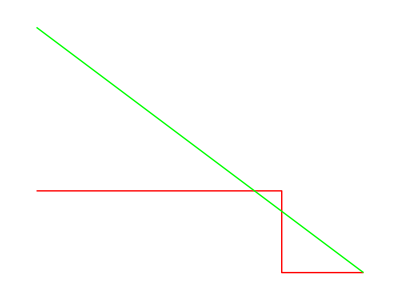

```mathematica
Graphics[{Red,
Line[{{661,568},{664,568},{664,567},{665,567}}],
Green,
Line[{{665,567},{661,570}}],
Black,PointSize[0.03],PointSize[0.01]}]
```

```mathematica
Graphics[{Red,
Line[{{46,37},{25,28}}],
Line[{{274,24},{46,37}}],
Line[{{46,37}, {34,38}, {53,40}}],
Line[{{53,40},{46,37}}],
Line[{{53,40},{54,40}}],
Line[{{54,40},{428,78}}],
Line[{{463,221},{54,40}}],
Line[{{46,40},{53,40}}],
Line[{{54,40}, {57,40}, {364,52}}],
Green,
Black,PointSize[0.03],PointSize[0.01]}]
```

-Graphics-

## testBug8

PLATFORMCONTROLLER.mc.pressed_M(new Point(56, 10));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(57, 11));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(58, 11));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(54, 11));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(54, 12));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(58, 11));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(56, 10));

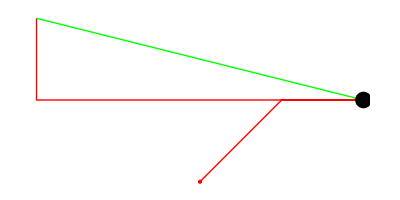

```mathematica
Graphics[{Red,
Line[{{56,10},{57,11},{58,11},{54,11},{54,12}}],
Green,
Line[{{54,12},{58,11}}],
Red,Point[{56,10}],Black,PointSize[0.03],Point[{58,11}],PointSize[0.01]}]
```

## testBug9

PLATFORMCONTROLLER.mc.pressed_M(new Point(775, 457));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(772, 467));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(772, 469));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(773, 465));
		PLATFORMCONTROLLER.mc.released_M(false);
		
		PLATFORMCONTROLLER.mc.pressed_M(new Point(773, 465));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(775, 457));
		PLATFORMCONTROLLER.mc.released_M(false);

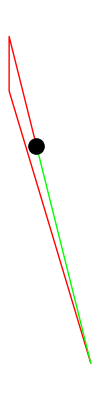

```mathematica
Graphics[{Red,
Line[{{775,457},{772,467},{772,469},{773,465}}],
Green,
Line[{{773,465},{775,457}}],
Red,Black,PointSize[0.03],Point[{773,465}],PointSize[0.01]}]
```

## testBug10

PLATFORMCONTROLLER.mc.pressed_M(new Point(775, 457));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(772, 467));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(772, 469));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(775, 457));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(778, 449));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(798, 448));
		PLATFORMCONTROLLER.mc.released_M(false);
		
		PLATFORMCONTROLLER.mc.pressed_M(new Point(798, 448));
		PLATFORMCONTROLLER.mc.dragged_M(new Point(760, 460));
		PLATFORMCONTROLLER.mc.released_M(false);

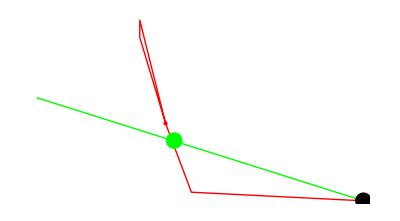

```mathematica
Graphics[{Red,
Line[{{775,457},{772,467},{772,469},{775,457},{778,449},{798,448}}],
Green,
Line[{{798,448},{760,460}}],
Red,Point[{775,457}],Black,PointSize[0.03],Point[{798,448}],Green,Point[{776,455}],PointSize[0.01]}]
```